```mathematica
Fa3[n_,a_,s_]:=(-1)^a((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
```

```mathematica
Fa3[n,1,0]
```

-1+n

```mathematica
Fa3[n,1,2]
```

1-1/n

```mathematica
Fa3[n,1,-1]
```

1/2 (-1+n^2)

```mathematica
Fa3[n,1,-2]
```

1/3 (-1+n^3)

```mathematica
Fa3[n,1,-3]
```

1/4 (-1+n^4)

```mathematica
Fa3[n,1,-1/2]
```

-2/3 (1-n^(3/2))

```mathematica
Fa3[n,1,1/2]
```

-2 (1-√n)

```mathematica
Fa3[n,2,0]
```

Gamma[2,0,-Log[n]]

```mathematica
Fa3[n,2,-1]
```

1/4 Gamma[2,0,-2 Log[n]]

```mathematica
Grid[Table[Fa3[n,aa,ss],{ss,-5,7},{aa,1,6}]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

1/6 (-1+n^6) | 1/36 Gamma[2,0,-6 Log[n]] | -1/432 Gamma[3,0,-6 Log[n]] | Gamma[4,0,-6 Log[n]]/7776 | -Gamma[5,0,-6 Log[n]]/186624 | Gamma[6,0,-6 Log[n]]/5598720
1/5 (-1+n^5) | 1/25 Gamma[2,0,-5 Log[n]] | -1/250 Gamma[3,0,-5 Log[n]] | Gamma[4,0,-5 Log[n]]/3750 | -Gamma[5,0,-5 Log[n]]/75000 | Gamma[6,0,-5 Log[n]]/1875000
1/4 (-1+n^4) | 1/16 Gamma[2,0,-4 Log[n]] | -1/128 Gamma[3,0,-4 Log[n]] | Gamma[4,0,-4 Log[n]]/1536 | -Gamma[5,0,-4 Log[n]]/24576 | Gamma[6,0,-4 Log[n]]/491520
1/3 (-1+n^3) | 1/9 Gamma[2,0,-3 Log[n]] | -1/54 Gamma[3,0,-3 Log[n]] | 1/486 Gamma[4,0,-3 Log[n]] | -Gamma[5,0,-3 Log[n]]/5832 | Gamma[6,0,-3 Log[n]]/87480
1/2 (-1+n^2) | 1/4 Gamma[2,0,-2 Log[n]] | -1/16 Gamma[3,0,-2 Log[n]] | 1/96 Gamma[4,0,-2 Log[n]] | -1/768 Gamma[5,0,-2 Log[n]] | Gamma[6,0,-2 Log[n]]/7680
-1+n | Gamma[2,0,-Log[n]] | -1/2 Gamma[3,0,-Log[n]] | 1/6 Gamma[4,0,-Log[n]] | -1/24 Gamma[5,0,-Log[n]] | 1/120 Gamma[6,0,-Log[n]]
Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate | Indeterminate
1-1/n | Gamma[2,0,Log[n]] | 1/2 Gamma[3,0,Log[n]] | 1/6 Gamma[4,0,Log[n]] | 1/24 Gamma[5,0,Log[n]] | 1/120 Gamma[6,0,Log[n]]
1/2 (1-1/n^2) | 1/4 Gamma[2,0,2 Log[n]] | 1/16 Gamma[3,0,2 Log[n]] | 1/96 Gamma[4,0,2 Log[n]] | 1/768 Gamma[5,0,2 Log[n]] | Gamma[6,0,2 Log[n]]/7680
1/3 (1-1/n^3) | 1/9 Gamma[2,0,3 Log[n]] | 1/54 Gamma[3,0,3 Log[n]] | 1/486 Gamma[4,0,3 Log[n]] | Gamma[5,0,3 Log[n]]/5832 | Gamma[6,0,3 Log[n]]/87480
1/4 (1-1/n^4) | 1/16 Gamma[2,0,4 Log[n]] | 1/128 Gamma[3,0,4 Log[n]] | Gamma[4,0,4 Log[n]]/1536 | Gamma[5,0,4 Log[n]]/24576 | Gamma[6,0,4 Log[n]]/491520
1/5 (1-1/n^5) | 1/25 Gamma[2,0,5 Log[n]] | 1/250 Gamma[3,0,5 Log[n]] | Gamma[4,0,5 Log[n]]/3750 | Gamma[5,0,5 Log[n]]/75000 | Gamma[6,0,5 Log[n]]/1875000
1/6 (1-1/n^6) | 1/36 Gamma[2,0,6 Log[n]] | 1/432 Gamma[3,0,6 Log[n]] | Gamma[4,0,6 Log[n]]/7776 | Gamma[5,0,6 Log[n]]/186624 | Gamma[6,0,6 Log[n]]/5598720

```mathematica
Expand[Sum[j^5,{j,2,n}]]
```

-1-n^2/12+(5 n^4)/12+n^5/2+n^6/6

```mathematica
Expand[Sum[j^(-2),{j,2,n}]]
```

-1+HarmonicNumber[n,2]

```mathematica
Grid[Table[Limit[(Fa3[n,a2,ss]-1)/a2,a2->aa],{ss,-2,4},{aa,-3,1}]]
```

Infinity::indet: Indeterminate expression 0\ (-∞) encountered.

28/3 | -4 | 4 | ⅈ π-Gamma[0,-3 Log[n]]-Log[3] | 1/3 (-4+n^3)
3 | -3/2 | 3 | ⅈ π-Gamma[0,-2 Log[n]]-Log[2] | 1/2 (-3+n^2)
2/3 | 0 | 2 | ⅈ π-Gamma[0,-Log[n]] | -2+n
1/3 | 1/2 | 1 | -∞ | 0
0 | 0 | 0 | -Gamma[0,Log[n]] | -1/n
-7/3 | -3/2 | -1 | -Gamma[0,2 Log[n]]-Log[2] | -(1+n^2)/(2 n^2)
-26/3 | -4 | -2 | -Gamma[0,3 Log[n]]-Log[3] | -2/3-1/(3 n^3)

```mathematica
Grid[Table[Limit[(Fa3[n,a2,ss]-1)/a2,a2->aa],{ss,-3,5},{aa,-6,3}]]
```

-1365/2 | 205 | -255/4 | 65/3 | -15/2 | 5 | ⅈ π-Gamma[0,-4 Log[n]]-Log[4] | 1/4 (-5+n^4) | 1/32 (-15-Gamma[2,-4 Log[n]]) | 1/384 (-130+Gamma[3,-4 Log[n]])
-364/3 | 244/5 | -20 | 28/3 | -4 | 4 | ⅈ π-Gamma[0,-3 Log[n]]-Log[3] | 1/3 (-4+n^3) | 1/18 (-8-Gamma[2,-3 Log[n]]) | 1/162 (-56+Gamma[3,-3 Log[n]])
-21/2 | 33/5 | -15/4 | 3 | -3/2 | 3 | ⅈ π-Gamma[0,-2 Log[n]]-Log[2] | 1/2 (-3+n^2) | 1/8 (-3-Gamma[2,-2 Log[n]]) | 1/48 (-18+Gamma[3,-2 Log[n]])
0 | 2/5 | 0 | 2/3 | 0 | 2 | ⅈ π-Gamma[0,-Log[n]] | -2+n | -1/2 Gamma[2,-Log[n]] | 1/6 (-4+Gamma[3,-Log[n]])
1/6 | 1/5 | 1/4 | 1/3 | 1/2 | 1 | -∞ | 0 | ComplexInfinity | ComplexInfinity
0 | 0 | 0 | 0 | 0 | 0 | -Gamma[0,Log[n]] | -1/n | -1/2 Gamma[2,Log[n]] | -1/6 Gamma[3,Log[n]]
-21/2 | -31/5 | -15/4 | -7/3 | -3/2 | -1 | -Gamma[0,2 Log[n]]-Log[2] | -(1+n^2)/(2 n^2) | 1/8 (-3-Gamma[2,2 Log[n]]) | 1/48 (-14-Gamma[3,2 Log[n]])
-364/3 | -242/5 | -20 | -26/3 | -4 | -2 | -Gamma[0,3 Log[n]]-Log[3] | -2/3-1/(3 n^3) | 1/18 (-8-Gamma[2,3 Log[n]]) | 1/162 (-52-Gamma[3,3 Log[n]])
-1365/2 | -1023/5 | -255/4 | -21 | -15/2 | -3 | -Gamma[0,4 Log[n]]-Log[4] | -3/4-1/(4 n^4) | 1/32 (-15-Gamma[2,4 Log[n]]) | 1/384 (-126-Gamma[3,4 Log[n]])

```mathematica
-Gamma[1,0,-Log[n]]
```

-1+n

```mathematica
-Gamma[1,0,-(1-N[ZetaZero[1]])Log[n]]-Gamma[1,0,-(1-N[ZetaZero[-1]])Log[n]]
```

```mathematica
aa[n_]:=-2.+n^(0.5-14.134725141734695 ⅈ)+n^(0.5+14.134725141734695 ⅈ)
```

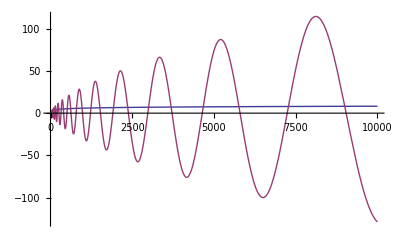

```mathematica
Plot[{Fa3[j,aa=2,bb=0]/j,Re[Fa3[j,aa,ZetaZero[cc=1]]+Fa3[j,aa,ZetaZero[-cc]]]},{j,1,10000}]
```

```mathematica
N[-Gamma[0,-Log[100]]]
```

30.1261+3.14159 ⅈ

```mathematica
N[LogIntegral[100]]
```

30.1261

```mathematica
N[-Gamma[0,-(1-ZetaZero[1])Log[100]]]- Pi I
```

0.116437-3.24171 ⅈ

```mathematica
N[LogIntegral[100^(1-ZetaZero[1])]]
```

1.35421-6.31436 ⅈ

```mathematica
N[ExpIntegralEi[(1-ZetaZero[1])Log[100]]]
```

0.116437-3.24171 ⅈ

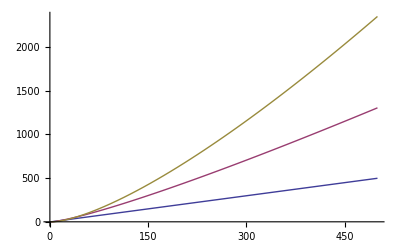

```mathematica
Plot[{(Fa3[n,1,0]-1)/1,(Fa3[n,2,0]-1)/2,(Fa3[n,3,0]-1)/3},{n,1,500}]
```

```mathematica
Limit[((-1)^a(Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a+1]-1/a,{a->0}]
```

{ⅈ π-Gamma[0,(-1+s) Log[n]]-Log[1-s]}

```mathematica
N[Gamma[3,0,-Log[100]]]
```

-1397.73+3.42834×10^-13 ⅈ

```mathematica
N[ (3-1)Gamma[3-1,0,-Log[100]]-(-Log[100])^(3-1) E^(-(-Log[100]))]
```

-1397.73-8.83012×10^-14 ⅈ

```mathematica
fz[n_,s_]:=(s-1)Gamma[s-1,0,n]-(n)^(s-1) E^(-n)
fz1[n_,s_]:=-(n)^(s-1) E^(-n)
```

```mathematica
N[fz[-Log[100],3]]
```

-1397.73-8.83012×10^-14 ⅈ

```mathematica
Limit[fz[-Log[n],a],{a->1}]
```

{1-n}

```mathematica
N[Sum[(1-k Log[k+1]+k Log[k])/k,{k,1,20000}]]
```

0.577191

```mathematica
Limit[1/n Sum[Ceiling[n/j]-n/j,{j,1,n}],n->Infinity]
```

$Aborted

```mathematica
Fa3a[n_,a_,s_]:=If[a==0,Limit[Fa3[n,b,s],{b->0}],Fa3[n,a,s]]
D2E2a[n_,k_,b_,s_]:= Sum[ (-1)^j b^(j(1-s)) Binomial[k,j] Sum[ Binomial[j,m] If[n/b^j<1,0,Fa3a[n/b^j,k-m,s]],{m,0,j}],{j,0,k}]

N[D2E2a[50,3,3,0]]
```

{-1.-9.81513×10^-16 ⅈ}

```mathematica
DiscretePlot[ Re[D2E2a[j,3,2,0]],{j,3,100}]
```

Map::level: Level specification {System`DiscretePlotDump`n} is not of the form n, {n}, or {m, n}.

Transpose::tperm: Permutation {2, 1} is longer than the dimensions {2} of the array.

Map::level: Level specification Transpose[{{{3}, {4}, {5}, {6}, {7}, {8}, {9}, {10}, {11}, {12}, {13}, {14}, {15}, {16}, {17}, {18}, {19}, {20}, {21}, {22}, {23}, {24}, {25}, {26}, {27}, {28}, {29}, {30}, {31}, {32}, {33}, {34}, {35}, {36}, {37}, {38}, {39}, {40}, {41}, {42}, {43}, {44}, {45}, {46}, {47}, {48}, {49}, {50}, {51}, {52}, « 48 »}, {System`DiscretePlotDump`n}}, {2, 1}] is not of the form n, {n}, or {m, n}.

General::stop: Further output of Map :: level will be suppressed during this calculation.

Transpose::tperm: Permutation {2, 1} is longer than the dimensions {2} of the array.

General::stop: Further output of Transpose :: tperm will be suppressed during this calculation.

Transpose::list: List expected at position 2 in Transpose[True, True].

MapThread::mptd: Object Map[Transpose[True, True], {True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, « 48 »}, Transpose[True, True]] at position {2, 1} in MapThread[And, {Map[Transpose[True, True], {True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, « 48 »}, Transpose[True, True]], Map[Charting`realNumericQ[If[SameQ[« 2 »] && Unequal[« 2 »], Table[Indeterminate, {« 1 »}], N[Slot[« 1 »], System`DiscretePlotDump`modelData$150676[« 1 »]]]] &, {True, True, True, True, True, False, « 39 », False, False, False, False, False, « 48 »}, {False}]}, 2] has only 0 of required 2 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Pick::incomp: Expressions {Map[If[Head[Slot[« 1 »]] === List && Length[Slot[« 1 »]] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$150676["WorkingPrecision"]]] &, {-0.225222, -1.58427, -0.147778, 1.7961, 4.19297, {7.}, {-1.}, {-1.}, « 35 », {-1.}, {-1.}, {-1.}, {-1.}, {-1.}, {-1.}, {-1.}, « 48 »}, {System`DiscretePlotDump`n}]} and {Map[Charting`realNumericQ[If[Head[« 1 »] === List && Length[« 1 »] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$150676["WorkingPrecision"]]]] &, {True, True, True, True, True, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, False, « 48 »}, {False}]} have incompatible shapes.

General::stop: Further output of Pick :: incomp will be suppressed during this calculation.

Set::shape: Lists {System`DiscretePlotDump`low, System`DiscretePlotDump`high} and « 1 » are not the same shape.

Transpose::list: List expected at position 2 in Transpose[If[Head[#1] === List && Length[#1] ≠ System`DiscretePlotDump`max, Table[Indeterminate, {System`DiscretePlotDump`max}], N[#1, System`DiscretePlotDump`modelData$150676["WorkingPrecision"]]] &, 1].

General::stop: Further output of Transpose :: list will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {Transpose[{}], Transpose[{}]} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[And, {{Map[Transpose[True, True], {True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, True, « 48 »}, Transpose[True, True]], Map[Charting`realNumericQ[If[And[« 2 »], Table[« 2 »], N[« 2 »]]] &, {True, True, True, True, True, False, False, False, False, False, False, False, False, « 25 », False, False, False, False, False, False, False, False, False, False, False, False, « 48 »}, {False}]}, {« 1 »}}]; dimensions are {2} and {98}.

Split::normal: Nonatomic expression expected at position 1 in Split[And].

Split::normal: Nonatomic expression expected at position 1 in Split[0].

First::normal: Nonatomic expression expected at position 1 in First[And].

Split::normal: Nonatomic expression expected at position 1 in Split[2].

General::stop: Further output of Split :: normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[2].

General::stop: Further output of First :: normal will be suppressed during this calculation.

-Graphics-

```mathematica
Fa3[100,0,-1]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
(-1)^a((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]/.{a->0,s->-1}
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
Gamma[0]
```

ComplexInfinity

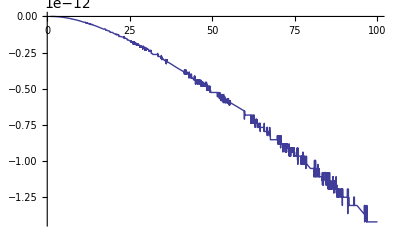

```mathematica
Plot[Re[Fa3[n,2.75,0]],{n,1,100}]
```

```mathematica
Fa3[n_,a_,s_]:=(-1)^a((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
Fa3b[n_,a_,s_]:=Abs[((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]]
Fa3c[n_,a_,s_]:=((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
```

```mathematica
N[Fa3[100,2.25,0]]
```

1.7053×10^-13+445.721 ⅈ

```mathematica
N[Fa3b[100,3,0]]
```

698.863

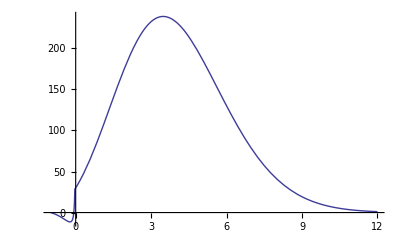

```mathematica
Plot[{(Fa3b[100,n,aa]-1)/n},{n,-1,12}]
```

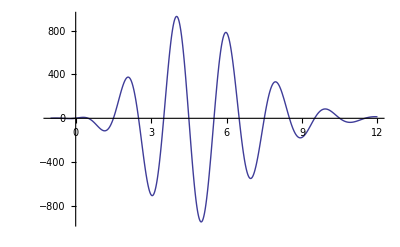

```mathematica
Plot[{(Re[Fa3c[100,n,aa=0]])},{n,-1,12}]
```

```mathematica
N[Fa3c[100,2,0]]
```

361.517-4.41506×10^-14 ⅈ

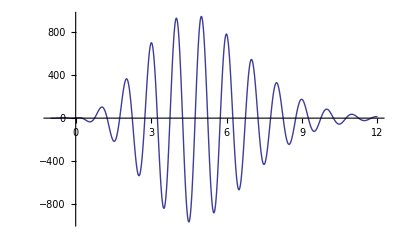

```mathematica
Plot[{(Re[Fa3[100,n,aa=0]])},{n,-1,12}]
```

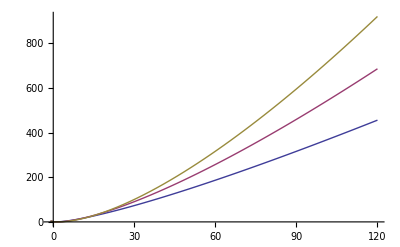

```mathematica
Plot[{Fa3b[n,2,aa],Fa3b[n,2.5,aa],Fa3b[n,3,aa]},{n,-1,120}]
```